## Evading the waterbed effect

show how to get around the Bode waterbed effect by adding passive isolation

```mathematica
Clear["Global`*"];
```

```mathematica
G=(1/(1+s))^2;k=Kp +Ki/s+ Kd s/(1+s/ωf);L=k G; S=1/(1+L);
T=L/(1+L); 
tmax=10; ϵ=10^-5; t1=t+ϵ;pars={Kp->10,Ki->3,Kd->7,ωf->10,l->2,d->1,ωff->5};
Gtf=TransferFunctionModel[G,s];  (* just the system *)
Stf=TransferFunctionModel[S,s]/.pars//Simplify;
Ttf =TransferFunctionModel[T,s]/.pars//Simplify;
Tfftf=TransferFunctionModel[T/(1+s/ωff),s]/.pars//Simplify;
```

Time-domain response.

```mathematica
Gbox[s_]:=ⅇ^(-l √(s/d))/.pars;{Gbox[s],Gboxtime=InverseLaplaceTransform[Gbox[s],s,t]}
```

{ⅇ^(-2 √s),ⅇ^(-1/t)/(√π t^(3/2))}

```mathematica
Gnobox=OutputResponse[Gtf,DiracDelta[t],{t,0,tmax}];
ybox=OutputResponse[Stf ,Gboxtime/.t->t1,{t,0,tmax}];

Gstep=OutputResponse[Gtf,UnitStep[t],{t,0,tmax}];
Tstep=OutputResponse[Ttf,UnitStep[t],{t,0,tmax}];
Tstepff=OutputResponse[Tfftf,UnitStep[t],{t,0,tmax}];
```

graphics

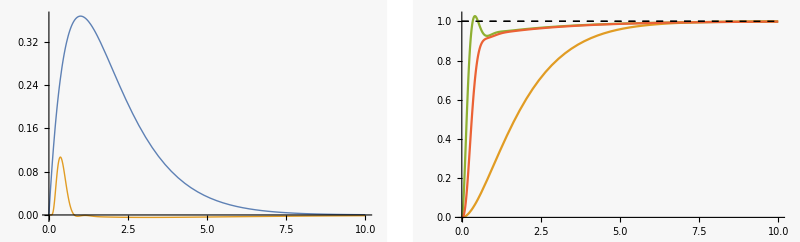

```mathematica
p1=Plot[{Gnobox,ybox},{t,0,tmax},PlotRange->All,ImagePadding->{{25,5},{15,5}}]//Quiet;
p2=Plot[{1,Gstep,Tstep,Tstepff,1},{t,0,tmax},PlotRange->All,PlotStyle->{{Thin,Black,Dashed},,,},ImagePadding->{{25,5},{15,5}}]//Quiet;
GraphicsRow[{p1,p2},ImageSize->{500}]
```

Export data

```mathematica
dt=0.01;alldat=Table[{Gnobox[[1]],ybox[[1]],Gstep[[1]],Tstep[[1]],Tstepff[[1]]},{t,ϵ,tmax,dt}]//Quiet;
(* 
SetDirectory[NotebookDirectory[]];Export["noWaterbed.dat",alldat]; 
*)
```

also look at frequency domain  (not used in book problem); could use to replace  Gboxtime

```mathematica
boxApprox0=PadeApproximant[Exp[-2 √s],{s,1/4,{2,2}}]//Simplify
```

(8 (2+17 s-4 s^2))/(ⅇ (7+112 s+208 s^2))

```mathematica
boxApprox=FullSimplify[ComplexExpand[Abs[boxApprox0/.s->ⅈ ω]],Assumptions->ω>0]
```

(8 √((4+305 ω^2+16 ω^4)/(49+9632 ω^2+43264 ω^4)))/ⅇ

```mathematica
boxExact=FullSimplify[ComplexExpand[Abs[ⅇ^(-2 √s)/.s->ⅈ ω]],Assumptions->ω>0]
```

ⅇ^(-√2 √ω)

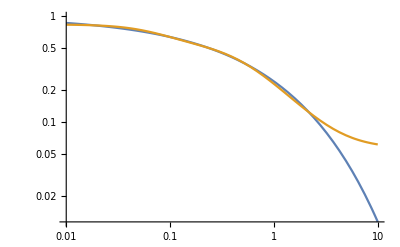

```mathematica
LogLogPlot[{boxExact,boxApprox},{ω,0.01,10}]
```